(3 ⅇ^(-9 t/100) Sin[1+3 x])/(50 (10/9+ⅇ^(-9 t/100) Cos[1+3 x]))

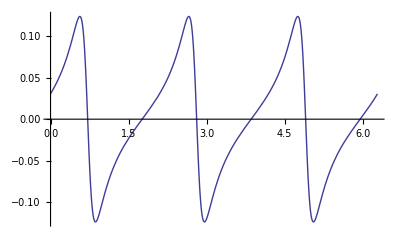

```mathematica
A = 1; (* Magnitude *)
B = 1; (* Phase Shift *)
Const = 10/9; (* Constant offset *)
ν = 1/100; (* Diffusion coefficient *)
μ = 3; (* Frequency *)
u[x_, t_] := A Exp[-ν μ^2 t] Cos[μ x + B] + Const (* Heat *)
w[x_, t_] = -2 ν D[u[x, t], x]/u[x, t]; (* Hopf-Cole *)
w[x,t]
GraphicsRow[{
Plot3D[w[x, t], {x, 0, 2 π}, {t, 0, 1}, PlotRange -> Full],
Plot3D[w[x, t], {x, 0, 2 π}, {t, 0, 1}, PlotRange -> Automatic],
Plot[w[x,0],{x,0,2π},PlotRange->Full]
}]
```

```mathematica
{FileNameSetter[Dynamic[filename],"Open"], Dynamic[filename]}
```

{Browse…,}

```mathematica
{uh,xh,th}=Map[
(Import[filename,{"Datasets",#} ])&,{"/u","/x","/t"}];
range =DataRange->{{Min[xh],Max[xh]},{Min[th],Max[th]}};

ListPlot3D[uh,range,PlotRange->Full]
ListPlot3D[uh,range,PlotRange->Automatic]
```

-Graphics3D-

-Graphics3D-

```mathematica
exact = Table[w[2π x,t],{t,th},{x,xh}];
error = exact - uh;
ListPlot3D[error,range,PlotRange->Full]
ListPlot3D[error,range,PlotRange->Automatic]
```

-Graphics3D-

-Graphics3D-

```mathematica
Manipulate[
ListPlot[{uh[[i]],exact[[i]](*,error[[i]]*)}],
{i,1,Dimensions[error][[1]],1}]
```

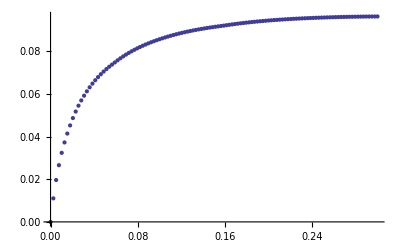

```mathematica
ListPlot[Max /@Abs[error],DataRange->{Min[th],Max[th]},PlotRange->Full]
```